# Industrial Robotics - Exam 07/01/2016

```mathematica
ClearAll[“Global`*”]
```

-Graphics-
The 3 degrees of freedom robot in the picture is composed of two revolute joints and a prismatic joint . The rotation q1 is performed about axis z0, q2 about axis z1 and the translation q3 (only positive) along axis z2 . When q1 = 0 axes x0 and z1 are aligned, when q2 = 0 axes x1 and x2 are aligned, when q3 = 0 axes x2 and x3 overlap .

### 1) Find the Jacobian matrix. Find and explain the singular configurations.

```mathematica
MrotZtrasl[α_,point_]:={{Cos[α],-Sin[α],0,point[[1]]},{Sin[α],Cos[α],0,point[[2]]},{0,0,1,point[[3]]},{0,0,0,1}};
```

Focus on RF1:

```mathematica
O1={0,0,L1,1};
M01p=MrotZtrasl[q1[t],O1];
M1p1=Transpose[{{0,1,0,0},{0,0,1,0},{1,0,0,0},{0,0,0,1}}];
M01=M01p.M1p1;
M01//MatrixForm
```

(-Sin[q1[t]] | 0 | Cos[q1[t]] | 0
Cos[q1[t]] | 0 | Sin[q1[t]] | 0
0 | 1 | 0 | L1
0 | 0 | 0 | 1)

Focus on RF2:

```mathematica
O2rf1={L2 Cos[q2[t]],L2 Sin[q2[t]],0,1};
M12=MrotZtrasl[q2[t],O2rf1];
M02=M01.M12;
M02//MatrixForm
```

(-Cos[q2[t]] Sin[q1[t]] | Sin[q1[t]] Sin[q2[t]] | Cos[q1[t]] | -L2 Cos[q2[t]] Sin[q1[t]]
Cos[q1[t]] Cos[q2[t]] | -Cos[q1[t]] Sin[q2[t]] | Sin[q1[t]] | L2 Cos[q1[t]] Cos[q2[t]]
Sin[q2[t]] | Cos[q2[t]] | 0 | L1+L2 Sin[q2[t]]
0 | 0 | 0 | 1)

Focus on RF3:

```mathematica
O3rf2={0,0,q3[t],1};
M23=MrotZtrasl[0,O3rf2];
M03=M02.M23;
M03//MatrixForm
```

(-Cos[q2[t]] Sin[q1[t]] | Sin[q1[t]] Sin[q2[t]] | Cos[q1[t]] | Cos[q1[t]] q3[t]-L2 Cos[q2[t]] Sin[q1[t]]
Cos[q1[t]] Cos[q2[t]] | -Cos[q1[t]] Sin[q2[t]] | Sin[q1[t]] | L2 Cos[q1[t]] Cos[q2[t]]+q3[t] Sin[q1[t]]
Sin[q2[t]] | Cos[q2[t]] | 0 | L1+L2 Sin[q2[t]]
0 | 0 | 0 | 1)

Jacobian

```mathematica
EE=M03[[1;;3,4]];
Jac=Simplify[D[EE,{{q1[t],q2[t],q3[t]}}]];
Jac//MatrixForm
```

(-L2 Cos[q1[t]] Cos[q2[t]]-q3[t] Sin[q1[t]] | L2 Sin[q1[t]] Sin[q2[t]] | Cos[q1[t]]
Cos[q1[t]] q3[t]-L2 Cos[q2[t]] Sin[q1[t]] | -L2 Cos[q1[t]] Sin[q2[t]] | Sin[q1[t]]
0 | L2 Cos[q2[t]] | 0)

Singular Configurations

```mathematica
detJac=Simplify[Det[Jac]]
```

L2 Cos[q2[t]] q3[t]

```mathematica
q2Singular=Solve[detJac==0,q2[t]]
```

{{q2[t]→ConditionalExpression[-π/2+2 π C[1], C[1]∈ℤ]},{q2[t]→ConditionalExpression[π/2+2 π C[1], C[1]∈ℤ]}}

```mathematica
q3Singular=Solve[detJac==0,q3[t]]
```

{{q3[t]→0}}

```mathematica
Jac/.q2[t]->π/2//MatrixForm
```

(-q3[t] Sin[q1[t]] | L2 Sin[q1[t]] | Cos[q1[t]]
Cos[q1[t]] q3[t] | -L2 Cos[q1[t]] | Sin[q1[t]]
0 | 0 | 0)

When π/2, the robot loses ability to generate velocity in the tangential direction (cannot generate velocity along ).

```mathematica
Jac/.q2[t]->-π/2//MatrixForm
```

(-q3[t] Sin[q1[t]] | -L2 Sin[q1[t]] | Cos[q1[t]]
Cos[q1[t]] q3[t] | L2 Cos[q1[t]] | Sin[q1[t]]
0 | 0 | 0)

When π/2, the robot behaves as in the case +π/2.

```mathematica
Jac/.q3[t]->0//MatrixForm
```

(-L2 Cos[q1[t]] Cos[q2[t]] | L2 Sin[q1[t]] Sin[q2[t]] | Cos[q1[t]]
-L2 Cos[q2[t]] Sin[q1[t]] | -L2 Cos[q1[t]] Sin[q2[t]] | Sin[q1[t]]
0 | L2 Cos[q2[t]] | 0)

When , col1 and col3 are linearly dependent, therefore the rank drops. Therefore, the rotational joints ( and ) can generate only a limited set of velocity. In particular, the velocity parallel to the vector formed by  is constant.

### 2) Find the joint coordinates which produce E coordinates in frame ^0√2,0,1 (assuming L1 = 1 m, L2 = 0.5 m), discard those which are not compatible with the robot structure and find the components in frame 0 of the z3 unit vector of the compatible solutions when E is in the required position.

```mathematica
lenData={L1->1,L2->0.5};
```

```mathematica
EEx=EE[[1]];EEy=EE[[2]];EEz=EE[[3]];
EExNum=EEx/.lenData;EEyNum=EEy/.lenData;EEzNum=EEz/.lenData;
```

```mathematica
allKinematicSol=Solve[{EExNum==√2,EEyNum==0,EEzNum==1},{q1[t],q2[t],q3[t]}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{q1[t]→-2.78023,q2[t]→0.,q3[t]→-1.32288},{q1[t]→2.78023,q2[t]→-3.14159,q3[t]→-1.32288},{q1[t]→2.78023,q2[t]→3.14159,q3[t]→-1.32288},{q1[t]→-0.361367,q2[t]→0.,q3[t]→1.32288},{q1[t]→0.361367,q2[t]→-3.14159,q3[t]→1.32288},{q1[t]→0.361367,q2[t]→3.14159,q3[t]→1.32288}}

```mathematica
KinematicSol=allKinematicSol[[{4,6}]]
```

{{q1[t]→-0.361367,q2[t]→0.,q3[t]→1.32288},{q1[t]→0.361367,q2[t]→3.14159,q3[t]→1.32288}}

Find OverHat[z3] w.r.t. RF0

```mathematica
z3UnitRF3={0,0,1,0};
z3UnitRF0=M03.z3UnitRF3;
z3UnitRF0=z3UnitRF0[[1;;3]];
z3UnitRF0//MatrixForm
(*Or use the M03's colums directly*)
M03[[1;;3,3]]
```

(Cos[q1[t]]
Sin[q1[t]]
0)

{Cos[q1[t]],Sin[q1[t]],0}

```mathematica
z3UnitRF0Num1=z3UnitRF0/.KinematicSol[[1]]
```

{0.935414,-0.353553,0}

```mathematica
z3UnitRF0Num2=z3UnitRF0/.KinematicSol[[2]]
```

{0.935414,0.353553,0}

### 3) The robot, starting still from zero joint coordinates, must bring the end effector to the position described above with zero final velocity by using constant acceleration motion profiles. Given amax1 = 2 rad/s2, amax2 = 2 rad/s2, amax3 = 3 m/s2, choose the joint coordinates which minimize the time. Rescale the motion profiles such that the joint actuators stop at the same time.

```mathematica
aMaxData={aMaxq1->2,aMaxq2->2,aMaxq3->3};
solTmin=Solve[Δq==2 1/2 aMax (T/2)^2,T]
```

{{T→-(2 √Δq)/(√aMax)},{T→(2 √Δq)/(√aMax)}}

```mathematica
Tmin[Δq_,aMax_]:=2 √(Abs[Δq]/aMax)
qValues={q1[t],q2[t],q3[t]}/.KinematicSol
```

{{-0.361367,0.,1.32288},{0.361367,3.14159,1.32288}}

```mathematica
(*For solution 1 of KinematicSol*)
Tt11=Tmin[qValues[[1,1]],aMaxq1]/.aMaxData;
Tt21=Tmin[qValues[[1,2]],aMaxq2]/.aMaxData;
Tt31=Tmin[qValues[[1,3]],aMaxq3]/.aMaxData;
Tmin1=Max[Tt11,Tt21, Tt31]
```

1.32809

```mathematica
(*For solution 2 of KinematicSol*)
Tt12=Tmin[qValues[[2,1]],aMaxq1]/.aMaxData;
Tt22=Tmin[qValues[[2,2]],aMaxq2]/.aMaxData;
Tt32=Tmin[qValues[[2,3]],aMaxq3]/.aMaxData;
Tmin2=Max[Tt12,Tt22, Tt32]
```

2.50663

```mathematica
Tf=Min[Tmin1,Tmin2]
```

1.32809

```mathematica
(*we choose sol1*)
q1f=q1[t]/.KinematicSol[[1]];
q2f=q2[t]/.KinematicSol[[1]];
q3f=q3[t]/.KinematicSol[[1]];
```

Rescale the accelerations.

```mathematica
aMaxrescaled=Solve[Δq==2 1/2 aMax (Tt/2)^2,aMax]
```

{{aMax→(4 Δq)/Tt^2}}

```mathematica
aMaxFormula[Δq_,Tt_]:=(4Δq)/Tt^2
```

```mathematica
aMax1Rescaled=aMaxFormula[q1f,Tf](*q1i=0*)
```

-0.819504

```mathematica
aMax2Rescaled=aMaxFormula[q2f,Tf]
```

0.

```mathematica
aMax3Rescaled=aMaxFormula[q3f,Tf]
```

3.

Define Triangular Profiles.

```mathematica
baseprofile=Piecewise[{{qin+1/2 a t^2,0<=t<=T/2},{qin+a T^2/4-((T-t)^2 a)/2,T/2<t<=T}}]
```

Piecewise[{{qin+(a t^2)/2, 0≤t≤T/2}, {qin+(a T^2)/4-1/2 a (-t+T)^2, T/2<t≤T}, {0, True}}]

```mathematica
q1Profile=baseprofile/.a->aMax1Rescaled/.qin->0/.T->Tf
```

Piecewise[{{-0.409752 t^2, 0≤t≤0.664047}, {-0.361367+0.409752 (1.32809-t)^2, 0.664047<t≤1.32809}, {0, True}}]

```mathematica
q2Profile=baseprofile/.a->aMax2Rescaled/.qin->0/.T->Tf
```

Piecewise[{{0., 0≤t≤0.664047||0.664047<t≤1.32809}, {0, True}}]

```mathematica
q3Profile=baseprofile/.a->aMax3Rescaled/.qin->0/.T->Tf
```

Piecewise[{{1.5 t^2, 0≤t≤0.664047}, {1.32288-1.5 (1.32809-t)^2, 0.664047<t≤1.32809}, {0, True}}]

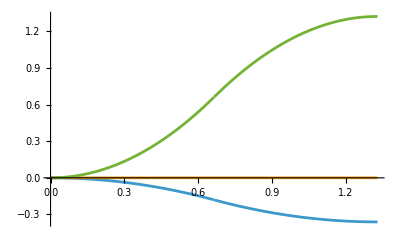

```mathematica
Plot[{q1Profile,q2Profile,q3Profile},{t,0,Tf}]
```

### 3) Links 1 and 2 can be approximated with lumped masses m1 and m2 located in G1 and G2 at half the length L1 and L2 of each link; link 3 is approximated by a lumped mass m3 located in G3 = E . The gravity force is present along - z0 . • Write the Lagrange function . • Calculate and plot (with scales) the torque and force time profiles required to perform the motion from the initial to the final configuration of point 3, assuming m1 = 10 kg, m2 = 5 kg, m3 = 3 kg .

```mathematica
massData={m1->10,m2->5,m3->3,g->9.81};
```

```mathematica
W01=Simplify[D[M01,t].Inverse[M01]];
W02=Simplify[D[M02,t].Inverse[M02]];
W03=Simplify[D[M03,t].Inverse[M03]];
```

```mathematica
J11={{0,0,0,0},{0,m1(-L1/2)^2,0,m1(-L1/2)},{0,0,0,0},{0,m1(-L1/2),0,m1}};
J22={{m2(-L2/2)^2,0,0,m2(-L2/2)},{0,0,0,0},{0,0,0,0},{m2(-L2/2),0,0,m2}};
J33={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,m3}};
```

```mathematica
J10=Simplify[M01.J11.Transpose[M01]];
J20=Simplify[M02.J22.Transpose[M02]];
J30=Simplify[M03.J33.Transpose[M03]];
```

Kinetic energy.

```mathematica
T1=Simplify[1/2 Tr[W01.J10.Transpose[W01]]]
```

0

```mathematica
T2=Simplify[1/2 Tr[W02.J20.Transpose[W02]]]
```

1/8 L2^2 m2 (Cos[q2[t]]^2 q1'[t]^2+q2'[t]^2)

```mathematica
T3=Simplify[1/2 Tr[W03.J30.Transpose[W03]]]
```

1/2 m3 ((L2^2 Cos[q2[t]]^2+q3[t]^2) q1'[t]^2+L2^2 q2'[t]^2+q3'[t]^2-2 L2 q1'[t] (q3[t] Sin[q2[t]] q2'[t]+Cos[q2[t]] q3'[t]))

Potential energy.

```mathematica
Hg1={{0,0,0,0},{0,0,0,0},{0,0,0,-g},{0,0,0,0}};
Hg2=Hg1;Hg3=Hg1;
```

```mathematica
Ug1=Tr[-Hg1.J10]
```

(g L1 m1)/2

```mathematica
Ug2=Tr[-Hg2.J20]
```

g (L1 m2+1/2 L2 m2 Sin[q2[t]])

```mathematica
Ug3=Tr[-Hg3.J30]
```

g m3 (L1+L2 Sin[q2[t]])

Lagrangian term.

```mathematica
Lagr=FullSimplify[T1+T2+T3-Ug1-Ug2-Ug3]
```

1/8 (-4 g L1 (m1+2 (m2+m3))-4 g L2 (m2+2 m3) Sin[q2[t]]+(L2^2 (m2+4 m3) Cos[q2[t]]^2+4 m3 q3[t]^2) q1'[t]^2+L2^2 (m2+4 m3) q2'[t]^2+4 m3 q3'[t]^2-8 L2 m3 q1'[t] (q3[t] Sin[q2[t]] q2'[t]+Cos[q2[t]] q3'[t]))

Equation 1:

```mathematica
dLagrdq1dotdt=Simplify[D[D[Lagr,q1'[t]],t]]
```

1/8 (2 q1'[t] (-L2^2 (m2+4 m3) Sin[2 q2[t]] q2'[t]+8 m3 q3[t] q3'[t])+2 (L2^2 (m2+4 m3) Cos[q2[t]]^2+4 m3 q3[t]^2) q1''[t]-8 L2 m3 (q3[t] (Cos[q2[t]] q2'[t]^2+Sin[q2[t]] q2''[t])+Cos[q2[t]] q3''[t]))

```mathematica
dLagrdq1=Simplify[D[Lagr,q1[t]]]
```

0

Equation 2:

```mathematica
dLagrdq2dotdt=Simplify[D[D[Lagr,q2'[t]],t]]
```

1/4 L2 (-4 m3 Sin[q2[t]] q1'[t] q3'[t]-4 m3 q3[t] (Cos[q2[t]] q1'[t] q2'[t]+Sin[q2[t]] q1''[t])+L2 (m2+4 m3) q2''[t])

```mathematica
dLagrdq2=Simplify[D[Lagr,q2[t]]]
```

-1/8 L2 (4 g (m2+2 m3) Cos[q2[t]]+L2 (m2+4 m3) Sin[2 q2[t]] q1'[t]^2+8 m3 q1'[t] (Cos[q2[t]] q3[t] q2'[t]-Sin[q2[t]] q3'[t]))

Equation 3:

```mathematica
dLagrdq3dotdt=Simplify[D[D[Lagr,q3'[t]],t]]
```

m3 (L2 Sin[q2[t]] q1'[t] q2'[t]-L2 Cos[q2[t]] q1''[t]+q3''[t])

```mathematica
dLagrdq3=Simplify[D[Lagr,q3[t]]]
```

m3 q1'[t] (q3[t] q1'[t]-L2 Sin[q2[t]] q2'[t])

Equation of Motion

```mathematica
equation1=dLagrdq1dotdt-dLagrdq1-C1//Simplify
```

1/8 (-8 C1+2 q1'[t] (-L2^2 (m2+4 m3) Sin[2 q2[t]] q2'[t]+8 m3 q3[t] q3'[t])+2 (L2^2 (m2+4 m3) Cos[q2[t]]^2+4 m3 q3[t]^2) q1''[t]-8 L2 m3 (q3[t] (Cos[q2[t]] q2'[t]^2+Sin[q2[t]] q2''[t])+Cos[q2[t]] q3''[t]))

```mathematica
equation2=dLagrdq2dotdt-dLagrdq2-C2//Simplify
```

1/8 (-8 C2+4 g L2 m2 Cos[q2[t]]+8 g L2 m3 Cos[q2[t]]+L2^2 (m2+4 m3) Sin[2 q2[t]] q1'[t]^2-16 L2 m3 Sin[q2[t]] q1'[t] q3'[t]-8 L2 m3 q3[t] Sin[q2[t]] q1''[t]+2 L2^2 m2 q2''[t]+8 L2^2 m3 q2''[t])

```mathematica
equation3=dLagrdq3dotdt-dLagrdq3-F3//Simplify
```

-F3-m3 q3[t] q1'[t]^2+2 L2 m3 Sin[q2[t]] q1'[t] q2'[t]-L2 m3 Cos[q2[t]] q1''[t]+m3 q3''[t]

Inverse Dynamics

```mathematica
C1InvDyn=C1/.Flatten[Solve[equation1==0,C1]]
```

1/4 (-L2^2 m2 Sin[2 q2[t]] q1'[t] q2'[t]-4 L2^2 m3 Sin[2 q2[t]] q1'[t] q2'[t]-4 L2 m3 Cos[q2[t]] q3[t] q2'[t]^2+8 m3 q3[t] q1'[t] q3'[t]+L2^2 m2 Cos[q2[t]]^2 q1''[t]+4 L2^2 m3 Cos[q2[t]]^2 q1''[t]+4 m3 q3[t]^2 q1''[t]-4 L2 m3 q3[t] Sin[q2[t]] q2''[t]-4 L2 m3 Cos[q2[t]] q3''[t])

```mathematica
C2InvDyn=C2/.Flatten[Solve[equation2==0,C2]]
```

1/8 (4 g L2 m2 Cos[q2[t]]+8 g L2 m3 Cos[q2[t]]+L2^2 m2 Sin[2 q2[t]] q1'[t]^2+4 L2^2 m3 Sin[2 q2[t]] q1'[t]^2-16 L2 m3 Sin[q2[t]] q1'[t] q3'[t]-8 L2 m3 q3[t] Sin[q2[t]] q1''[t]+2 L2^2 m2 q2''[t]+8 L2^2 m3 q2''[t])

```mathematica
F3InvDyn=F3/.Flatten[Solve[equation3==0,F3]]
```

-m3 q3[t] q1'[t]^2+2 L2 m3 Sin[q2[t]] q1'[t] q2'[t]-L2 m3 Cos[q2[t]] q1''[t]+m3 q3''[t]

Plot Torques (& Forces) Profiles

```mathematica
C1InvDynNum=C1InvDyn/.lenData/.massData/.q1[t]->q1Profile/.q1'[t]->D[q1Profile,t]/.q1''[t]->D[q1Profile,t,t]/.q2[t]->q2Profile/.q2'[t]->D[q2Profile,t]/.q2''[t]->D[q2Profile,t,t]/.q3[t]->q3Profile/.q3'[t]->D[q3Profile,t]/.q3''[t]->D[q3Profile,t,t]
```

1/4 (0.+4.25 Cos[Piecewise[{{0., 0≤t≤0.664047||0.664047<t≤1.32809}, {0, True}}]]^2 (Piecewise[{{0, t<0}, {-0.819504, 0<t<55037753/82882303}, {0.819504, 55037753/82882303<t<86200917/64905725}, {0, t>86200917/64905725}, {Indeterminate, True}}])+12 (Piecewise[{{1.5 t^2, 0≤t≤0.664047}, {1.32288-1.5 (1.32809-t)^2, 0.664047<t≤1.32809}, {0, True}}])^2 (Piecewise[{{0, t<0}, {-0.819504, 0<t<55037753/82882303}, {0.819504, 55037753/82882303<t<86200917/64905725}, {0, t>86200917/64905725}, {Indeterminate, True}}])-6. Cos[Piecewise[{{0., 0≤t≤0.664047||0.664047<t≤1.32809}, {0, True}}]] (Piecewise[{{0, t<0}, {3., 0<t<55037753/82882303}, {-3., 55037753/82882303<t<86200917/64905725}, {0, t>86200917/64905725}, {Indeterminate, True}}])+24 (Piecewise[{{1.5 t^2, 0≤t≤0.664047}, {1.32288-1.5 (1.32809-t)^2, 0.664047<t≤1.32809}, {0, True}}]) (Piecewise[{{0, t<0||t==0}, {-0.819504 t, 0<t<55037753/82882303}, {-0.544189, t==55037753/82882303}, {0.409752 (-2.65619+2 t), 55037753/82882303<t<86200917/64905725}, {0, t>86200917/64905725}, {Indeterminate, True}}]) (Piecewise[{{0, t<0||t==0}, {3. t, 0<t<55037753/82882303}, {1.99214, t==55037753/82882303}, {-1.5 (-2.65619+2 t), 55037753/82882303<t<86200917/64905725}, {0, t>86200917/64905725}, {Indeterminate, True}}]))

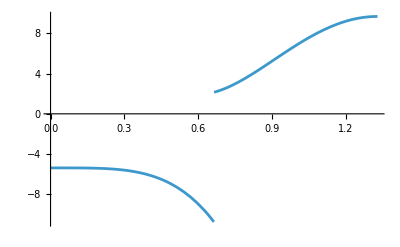

```mathematica
Plot[C1InvDynNum,{t,0,Tf}]
```

```mathematica
C2InvDynNum=C2InvDyn/.lenData/.massData/.q1[t]->q1Profile/.q1'[t]->D[q1Profile,t]/.q1''[t]->D[q1Profile,t,t]/.q2[t]->q2Profile/.q2'[t]->D[q2Profile,t]/.q2''[t]->D[q2Profile,t,t]/.q3[t]->q3Profile/.q3'[t]->D[q3Profile,t]/.q3''[t]->D[q3Profile,t,t]
```

1/8 (0.+215.82 Cos[Piecewise[{{0., 0≤t≤0.664047||0.664047<t≤1.32809}, {0, True}}]]-12. (Piecewise[{{1.5 t^2, 0≤t≤0.664047}, {1.32288-1.5 (1.32809-t)^2, 0.664047<t≤1.32809}, {0, True}}]) (Piecewise[{{0, t<0}, {-0.819504, 0<t<55037753/82882303}, {0.819504, 55037753/82882303<t<86200917/64905725}, {0, t>86200917/64905725}, {Indeterminate, True}}]) Sin[Piecewise[{{0., 0≤t≤0.664047||0.664047<t≤1.32809}, {0, True}}]]-24. (Piecewise[{{0, t<0||t==0}, {-0.819504 t, 0<t<55037753/82882303}, {-0.544189, t==55037753/82882303}, {0.409752 (-2.65619+2 t), 55037753/82882303<t<86200917/64905725}, {0, t>86200917/64905725}, {Indeterminate, True}}]) (Piecewise[{{0, t<0||t==0}, {3. t, 0<t<55037753/82882303}, {1.99214, t==55037753/82882303}, {-1.5 (-2.65619+2 t), 55037753/82882303<t<86200917/64905725}, {0, t>86200917/64905725}, {Indeterminate, True}}]) Sin[Piecewise[{{0., 0≤t≤0.664047||0.664047<t≤1.32809}, {0, True}}]]+4.25 (Piecewise[{{0, t<0||t==0}, {-0.819504 t, 0<t<55037753/82882303}, {-0.544189, t==55037753/82882303}, {0.409752 (-2.65619+2 t), 55037753/82882303<t<86200917/64905725}, {0, t>86200917/64905725}, {Indeterminate, True}}])^2 Sin[2 (Piecewise[{{0., 0≤t≤0.664047||0.664047<t≤1.32809}, {0, True}}])])

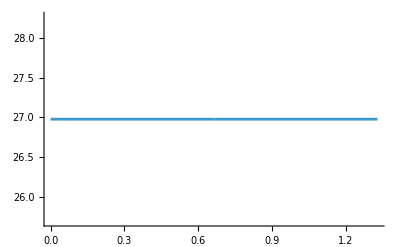

```mathematica
Plot[C2InvDynNum,{t,0,Tf}]
```

```mathematica
F3InvDynNum=F3InvDyn/.lenData/.massData/.q1[t]->q1Profile/.q1'[t]->D[q1Profile,t]/.q1''[t]->D[q1Profile,t,t]/.q2[t]->q2Profile/.q2'[t]->D[q2Profile,t]/.q2''[t]->D[q2Profile,t,t]/.q3[t]->q3Profile/.q3'[t]->D[q3Profile,t]/.q3''[t]->D[q3Profile,t,t]
```

0.-1.5 Cos[Piecewise[{{0., 0≤t≤0.664047||0.664047<t≤1.32809}, {0, True}}]] (Piecewise[{{0, t<0}, {-0.819504, 0<t<55037753/82882303}, {0.819504, 55037753/82882303<t<86200917/64905725}, {0, t>86200917/64905725}, {Indeterminate, True}}])+3 (Piecewise[{{0, t<0}, {3., 0<t<55037753/82882303}, {-3., 55037753/82882303<t<86200917/64905725}, {0, t>86200917/64905725}, {Indeterminate, True}}])-3 (Piecewise[{{1.5 t^2, 0≤t≤0.664047}, {1.32288-1.5 (1.32809-t)^2, 0.664047<t≤1.32809}, {0, True}}]) (Piecewise[{{0, t<0||t==0}, {-0.819504 t, 0<t<55037753/82882303}, {-0.544189, t==55037753/82882303}, {0.409752 (-2.65619+2 t), 55037753/82882303<t<86200917/64905725}, {0, t>86200917/64905725}, {Indeterminate, True}}])^2

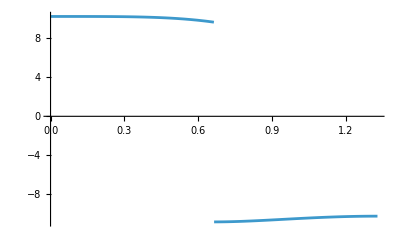

```mathematica
Plot[F3InvDynNum,{t,0,Tf}]
```